```mathematica
fs={Frame->True, FrameStyle->Black};
ps={PlotStyle->Directive[Black]};
bs={BaseStyle->{FontSize->16}};
```

```mathematica
a=0.01;x0=5.;tmax=20.;
```

```mathematica
,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","DifferenceOrder"->"Pseudospectral","MinStepSize"->0.2}}
```

```mathematica
nlse=NDSolveValue[Evaluate[{I D[u[t,x],t]+D[u[t,x],x,x]+2 Abs[u[t,x]]^2 u[t,x]==0.1 (1-Cos[Pi x/x0]),u[0,x]==ⅇ^(-(x-a)^2)+ⅇ^(-(x+a)^2),u[t,-x0]==u[t,x0]}],u,{t,0,tmax},{x,-x0,x0},MaxSteps->Infinity,PrecisionGoal->3]
```

NDSolveValue::eerr: Warning: scaled local spatial error estimate of 21.6389 at t = 20. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 45 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

InterpolatingFunction[{{0., 20.}, {…, -5., 5., …}}, <>]

```mathematica
Plot3D[Re[nlse[t,x]],{t,0.,17.},{x,-5.,5.},PlotRange->All]
```

-Graphics3D-

```mathematica
,Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid"}}
```

```mathematica
b0=.5;tmax=200.;
nlse=NDSolveValue[Evaluate[{I D[u[t,x],t]-0.125D[u[t,x],x,x]- Abs[u[t,x]]^2 u[t,x]==0,u[0,x]==b0 (1-Cos[2 π x]),u[t,-x0]==u[t,x0]}],u,{t,0,tmax},{x,-x0,x0},MaxSteps->Infinity]
```

InterpolatingFunction[{{0., 200.}, {…, -5., 5., …}}, <>]

```mathematica
Plot3D[Re[nlse[t,x]],{t,0.,tmax},{x,-x0,x0},PlotPoints->50,MeshStyle->Thick,ColorFunction->Function[{x,y,z},ColorData["Rainbow"][z/12]],ColorFunctionScaling->False,PlotRange->{All,All,{-1,1}}]
```

-Graphics3D-

```mathematica
nDivs=250.;
nlseTable=Re[
Table[
Table[
nlse[t,x],{x,-x0,x0,2x0/nDivs}],{t,0,tmax,tmax/nDivs}]
];
```

```mathematica
dims=Dimensions[nlseTable][[1]]

normTable=Table[
Norm[
nlseTable[[i+1]]-nlseTable[[i]],2],
{i,1,dims-1,1}];
```

251

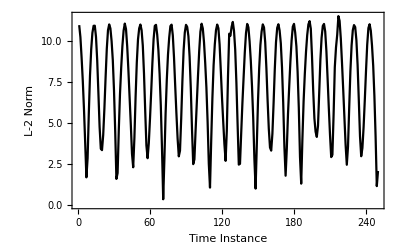

```mathematica
ListLinePlot[normTable,fs, ps,bs,
FrameLabel->{"Time Instance","L-2 Norm"}]
```